```mathematica
ponto = Import["C:\\Users\\Elton\\source\\Repos\\Projeto-SistemaNãoLinear-MS211\\Resultados\\h10E-5.csv"]
```

{{1,-1.2},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1}}

```mathematica
seta = Table[Arrow[{ponto[[i]],ponto[[i+1]]}],{i,1,Length[ponto]-1}]
```

{Arrow[{{1,-1.2},{1,1}}],Arrow[{{1,1},{1,1}}],Arrow[{{1,1},{1,1}}],Arrow[{{1,1},{1,1}}],Arrow[{{1,1},{1,1}}],Arrow[{{1,1},{1,1}}],Arrow[{{1,1},{1,1}}],Arrow[{{1,1},{1,1}}],Arrow[{{1,1},{1,1}}],Arrow[{{1,1},{1,1}}],Arrow[{{1,1},{1,1}}],Arrow[{{1,1},{1,1}}],Arrow[{{1,1},{1,1}}],Arrow[{{1,1},{1,1}}],Arrow[{{1,1},{1,1}}],Arrow[{{1,1},{1,1}}],Arrow[{{1,1},{1,1}}],Arrow[{{1,1},{1,1}}],Arrow[{{1,1},{1,1}}],Arrow[{{1,1},{1,1}}],Arrow[{{1,1},{1,1}}],Arrow[{{1,1},{1,1}}],Arrow[{{1,1},{1,1}}],Arrow[{{1,1},{1,1}}],Arrow[{{1,1},{1,1}}],Arrow[{{1,1},{1,1}}],Arrow[{{1,1},{1,1}}],Arrow[{{1,1},{1,1}}],Arrow[{{1,1},{1,1}}],Arrow[{{1,1},{1,1}}],Arrow[{{1,1},{1,1}}],Arrow[{{1,1},{1,1}}],Arrow[{{1,1},{1,1}}],Arrow[{{1,1},{1,1}}],Arrow[{{1,1},{1,1}}],Arrow[{{1,1},{1,1}}],Arrow[{{1,1},{1,1}}],Arrow[{{1,1},{1,1}}],Arrow[{{1,1},{1,1}}],Arrow[{{1,1},{1,1}}],Arrow[{{1,1},{1,1}}],Arrow[{{1,1},{1,1}}],Arrow[{{1,1},{1,1}}],Arrow[{{1,1},{1,1}}],Arrow[{{1,1},{1,1}}],Arrow[{{1,1},{1,1}}],Arrow[{{1,1},{1,1}}],Arrow[{{1,1},{1,1}}],Arrow[{{1,1},{1,1}}],Arrow[{{1,1},{1,1}}],Arrow[{{1,1},{1,1}}]}

VectorPlot::argr: VectorPlot called with 1 argument; 3 arguments are expected.

VectorPlot[seta]

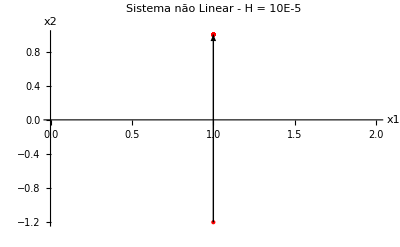

```mathematica
grafico = Show[ListPlot[ponto, PlotStyle->{Red,PointSize[Large]}],Graphics[seta], PlotLabel->"Sistema não Linear - H = 10E-5", AxesLabel->{"x1","x2"}]
```

```mathematica
Export["grafico10E-5.png", grafico]
```

grafico10E-5.png